# Ques_02: Elementary functions.

Let

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);       g[x_]:=x;     h[x_]:=Sin[x/3] - Cos[x^3/5]
```

1. Introduce the above functions and do the graph using the Plot command. Choose a reasonable interval for the values of x .

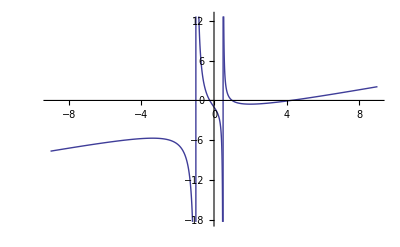

```mathematica
Plot[f[x],{x,-9,9}]
```

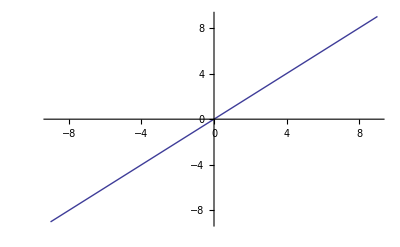

```mathematica
Plot[g[x],{x,-9,9}]
```

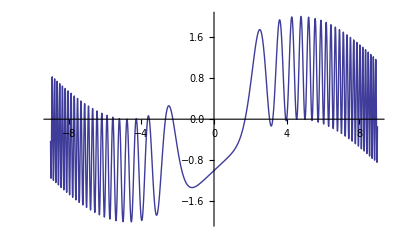

```mathematica
Plot[h[x],{x,-9,9}]
```

2 .	g(x) is the  bisectrix of the first quadrant. Represent the graph of f(x) and g(x) in the same graph. There are three crossing points between both functions. Obtain graphically the point which is further away from the origin of the axis.

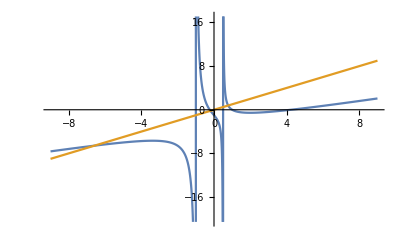

```mathematica
AA= Plot[{f[x],g[x]},{x,-9,9}]
```

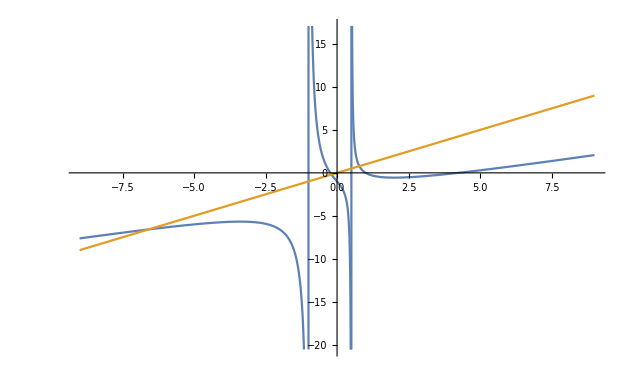

```mathematica
{Graphics[AA,ImageSize->100],Dynamic[MousePosition["Graphics","Mouse not in graphics!"]]}
```

Coordinate s of the point x= -6.585    , y=        -6.585

3. 	Calculate the asymptotes of f[x]

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);
```

```mathematica
Plot[f[x],{x,-9,9}]
```

-Graphics-

```mathematica
Solve[2 x^2+x-1==0,x]
```

{{x→-1},{x→1/2}}

Now You can write the vertical asymptotes or if you prefer you can do the limit o the limit with direction

```mathematica
vertical asymptotes at {{x->-1},{x->1/2}}
```

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->1/2]
```

∞

right

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->1/2,Direction->1]
```

-∞

left

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->1/2,Direction->-1]
```

∞

vertical asymptotes for a rational function, points where the denominator of the function is zero

```mathematica
vertical asymptotes at {{x->-1},{x->1/2}}
```

```mathematica
Solve[x^3-5 x^2+3x+1==0,x]
```

{{x→1},{x→2-√5},{x→2+√5}}

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->+∞]
```

∞

```mathematica
Limit[(x^3-5 x^2+3x+1)/(2 x^2+x-1),x->-∞]
```

-∞

oblique asymptotes, use the formula of the tutorial

```mathematica
m=Limit[((x^3-5 x^2+3x+1)/(2 x^2+x-1))/x,x->-∞]
```

1/2

```mathematica
n=Limit[((x^3-5 x^2+3x+1)/(2 x^2+x-1))-m x,x->-∞]
```

-11/4

```mathematica
AsyOb[x_]:=1/2 x -11/4
```

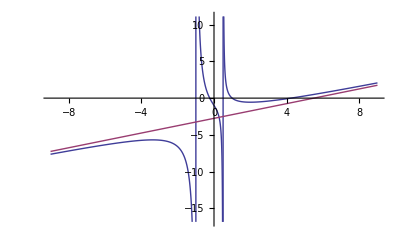

```mathematica
Plot[{     (x^3-5 x^2+3x+1)/(2 x^2+x-1),1/2 x -11/4},{x,-9,9}]
```

vertical  asymptotes:  x=-1       ; x=1/2
                                 oblique asymptote: y=1/2 x -11/4

4. 	Determine the symmetries of the functions f(x), g(x) and h(x), calculating  f(-x), g(-x) and h(-x). Obtain as a conclusion the symmetry of each function (pair, odd or neither).

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);       g[x_]:=x;     h[x_]:=Sin[x/3] - Cos[x^3/5]
```

```mathematica
f[-x]
```

(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)

```mathematica
Simplify[f[x]-f[-x]]
```

(4 x (-2+5 x^2+x^4))/(1-5 x^2+4 x^4)

```mathematica
g[-x]
```

-x

```mathematica
Simplify[g[x]-g[-x]]
```

2 x

If you look at the plot you can have doubts about symmetries with h[x], but you can see that if you substitute one point like x=3  and x=-3 at the function you can realize that you don’t have any kind of symmetries.

```mathematica
N[h[3]]
```

0.206778

```mathematica
N[h[-3]]
```

-1.47616

```mathematica
h[-x]
```

-Cos[x^3/5]-Sin[x/3]

```mathematica
Simplify[h[x]-h[-x]]
```

2 Sin[x/3]

f(x) is   neither
                                     g(x) is     odd  
                                    h(x) is     neither